```mathematica
Clear["Global`*"]
```

```mathematica
B1={{1,0,0,0},{0,0,0,0},{0,0,0,0},{0,0,0,-1}};
B2={{0,0,0,1},{0,0,0,0},{0,0,0,0},{1,0,0,0}};
```

```mathematica
H=ω*B1+B2;
```

```mathematica
Eigensystem[H]
```

{{0,0,-√(1+ω^2),√(1+ω^2)},{{0,0,1,0},{0,1,0,0},{ω-√(1+ω^2),0,0,1},{ω+√(1+ω^2),0,0,1}}}

```mathematica
U={{ω-√(1+ω^2),0,0,1},{0,0,1,0},{0,1,0,0},{ω+√(1+ω^2),0,0,1}};
```

```mathematica
P=1/4*{{1+2*(b1+b5),0,0,2*(b2-I*b3)},{0,1-2*(b5-b4),0,0},{0,0,1-2*(b5+b4),0},{2*(b2+I*b3),0,0,1+2*(b5-b1)}};
```

```mathematica
b1=(ω*e-l)/(ω^2+1);
b2=(e+ω*l)/(ω^2+1);
b3=c/(Sqrt[ω^2+1]);
b4=v/(Sqrt[ω^2+1]);
b5=d/(Sqrt[ω^2+1]);
```

```mathematica
ρ=U.P.Inverse[U]
```

{{((ω+√(1+ω^2)) (1/2 ((e+l ω)/(1+ω^2)-(ⅈ c)/(√(1+ω^2))) (ω-√(1+ω^2))+1/4 (1+2 (-(-l+e ω)/(1+ω^2)+d/(√(1+ω^2))))))/(2 √(1+ω^2))-(1/2 ((e+l ω)/(1+ω^2)+(ⅈ c)/(√(1+ω^2)))+1/4 (ω-√(1+ω^2)) (1+2 ((-l+e ω)/(1+ω^2)+d/(√(1+ω^2)))))/(2 √(1+ω^2)),0,0,((-ω+√(1+ω^2)) (1/2 ((e+l ω)/(1+ω^2)-(ⅈ c)/(√(1+ω^2))) (ω-√(1+ω^2))+1/4 (1+2 (-(-l+e ω)/(1+ω^2)+d/(√(1+ω^2))))))/(2 √(1+ω^2))+(1/2 ((e+l ω)/(1+ω^2)+(ⅈ c)/(√(1+ω^2)))+1/4 (ω-√(1+ω^2)) (1+2 ((-l+e ω)/(1+ω^2)+d/(√(1+ω^2)))))/(2 √(1+ω^2))},{0,1/4 (1-2 (d/(√(1+ω^2))+v/(√(1+ω^2)))),0,0},{0,0,1/4 (1-2 (d/(√(1+ω^2))-v/(√(1+ω^2)))),0},{((ω+√(1+ω^2)) (1/2 ((e+l ω)/(1+ω^2)-(ⅈ c)/(√(1+ω^2))) (ω+√(1+ω^2))+1/4 (1+2 (-(-l+e ω)/(1+ω^2)+d/(√(1+ω^2))))))/(2 √(1+ω^2))-(1/2 ((e+l ω)/(1+ω^2)+(ⅈ c)/(√(1+ω^2)))+1/4 (ω+√(1+ω^2)) (1+2 ((-l+e ω)/(1+ω^2)+d/(√(1+ω^2)))))/(2 √(1+ω^2)),0,0,((-ω+√(1+ω^2)) (1/2 ((e+l ω)/(1+ω^2)-(ⅈ c)/(√(1+ω^2))) (ω+√(1+ω^2))+1/4 (1+2 (-(-l+e ω)/(1+ω^2)+d/(√(1+ω^2))))))/(2 √(1+ω^2))+(1/2 ((e+l ω)/(1+ω^2)+(ⅈ c)/(√(1+ω^2)))+1/4 (ω+√(1+ω^2)) (1+2 ((-l+e ω)/(1+ω^2)+d/(√(1+ω^2)))))/(2 √(1+ω^2))}}

```mathematica
FullSimplify[MatrixForm[ρ]]
```

((2 d-2 e+√(1+ω^2))/(4 √(1+ω^2)) | 0 | 0 | ((ⅈ c+l) (-ω+√(1+ω^2)))/(2 √(1+ω^2))
0 | (-2 (d+v)+√(1+ω^2))/(4 √(1+ω^2)) | 0 | 0
0 | 0 | (-2 d+2 v+√(1+ω^2))/(4 √(1+ω^2)) | 0
((-ⅈ c+l) (ω+√(1+ω^2)))/(2 √(1+ω^2)) | 0 | 0 | (2 (d+e)+√(1+ω^2))/(4 √(1+ω^2)))

# Numerische Untersuchung Steuerung von zwei gleichartigen Spin-Systemen

-Graphics3D-

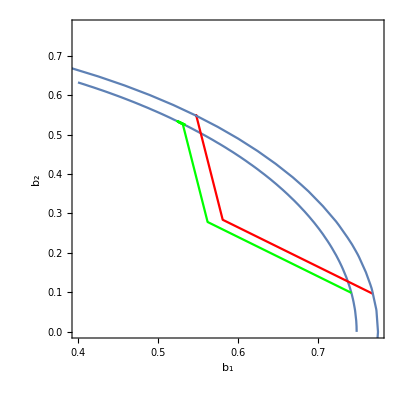

-Graphics3D-

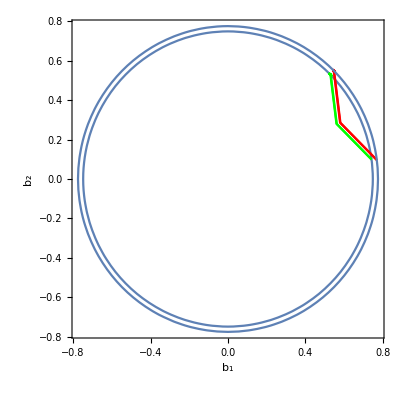

-Graphics3D-

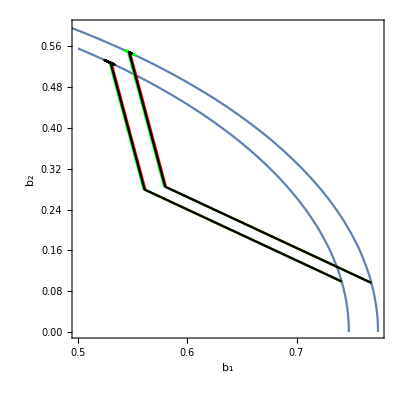

```mathematica
t1[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w1^2+1])*ArcSec[(w2-w1)*(w1-wi)/((1+w1*w2)*(1+w1*wi)-Sqrt[wi^2+1]/Sqrt[wf^2+1]*(1+w1^2)*(1+w2*wf))];
t2[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w2^2+1])*ArcSec[(w1-w2)*(wf-w2)/((1+w2^2)*Sqrt[wf^2+1]/Sqrt[wi^2+1]*(1+w1*wi)-(1+w1*w2)*(1+w2*wf))];
(*ω[w1_,w2_,t_,t1_,t2_]:= HeavisideTheta[t1-t]*w1+HeavisideTheta[t-t1]*w2;*)
ω[w1_,w2_,t_,t1_,t2_]:= HeavisideTheta[t1-t]*w1+HeavisideTheta[(t1+t2)-t]*HeavisideTheta[t-t1]*w2+HeavisideTheta[t-(t1+t2)]*w1;
Subscript[w, 1i]=8;
Subscript[w, 2i]=7.5;
Subscript[w, f]=1;
Subscript[w, min]=8;
Subscript[w, max]=1;
X1=0.6;
j1=1.002885;
j2=0.1742622232216704;
Temperature=Sqrt[Subscript[w, 1i]^2+1]/(ArcTanh[-Sqrt[X1]]);
X2=(Tanh[Sqrt[Subscript[w, 2i]^2+1]/Temperature])^2;
E10=Sqrt[X1*(Subscript[w, 1i]^2+1)];
E20=Sqrt[X2*(Subscript[w, 2i]^2+1)];
sol1=NDSolve[{x1'[t]==2*z1[t],y1'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z1[t],z1'[t]==-2*x1[t]+2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y1[t],x2'[t]==2*z2[t],y2'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z2[t],z2'[t]==-2*x2[t]+2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y2[t],x1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1),y1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1)/Subscript[w, 1i],z1[0]==0,x2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1),y2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1)/Subscript[w, 2i],z2[0]==0},{x1,y1,z1,x2,y2,z2},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},MaxSteps->∞];
Show[{ContourPlot3D[x^2+y^2+z^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]},{z,-Sqrt[X1],Sqrt[X1]},ContourStyle->{Opacity[0.25],Green},Mesh->None,AxesLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold],Style["b_3",Large,Bold]}],ContourPlot3D[x^2+y^2+z^2==X2,{x,-Sqrt[X2],Sqrt[X2]},{y,-Sqrt[X2],Sqrt[X2]},{z,-Sqrt[X2],Sqrt[X2]},ContourStyle->{Opacity[1],Yellow},Mesh->None,AxesLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold],Style["b_3",Large,Bold]}],ParametricPlot3D[{Evaluate[{x1[t],y1[t],z1[t]}/.sol1],Evaluate[{x2[t],y2[t],z2[t]}/.sol1]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Red]}]
Show[{ContourPlot[x^2+y^2==X2,{x,0.4,Sqrt[X1]},{y,0,Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol1]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green},AxesOrigin->{0,0},TicksStyle->{16,16}],
ContourPlot[x^2+y^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]}]
},FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},FrameTicks->{{0.4,0.5,0.6,0.7},Automatic,None,None},FrameTicksStyle->Directive[16],RotateLabel->False]
sol2=NDSolve[{x1'[t]==2*z1[t],y1'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*z1[t],z1'[t]==-2*x1[t]+2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*y1[t],x2'[t]==2*z2[t],y2'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*z2[t],z2'[t]==-2*x2[t]+2*ω[Subscript[w, max],Subscript[w, min],t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*y2[t],x1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1),y1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1)/Subscript[w, 1i],z1[0]==0,x2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1),y2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1)/Subscript[w, 2i],z2[0]==0},{x1,y1,z1,x2,y2,z2},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+10},MaxSteps->∞];
Show[{ContourPlot3D[x^2+y^2+z^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]},{z,-Sqrt[X1],Sqrt[X1]},ContourStyle->{Opacity[0.25],Green},Mesh->None,AxesLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic],Style["b_3",18,Italic]},AxesStyle->Directive[FontSize->16]],ContourPlot3D[x^2+y^2+z^2==X2,{x,-Sqrt[X2],Sqrt[X2]},{y,-Sqrt[X2],Sqrt[X2]},{z,-Sqrt[X2],Sqrt[X2]},ContourStyle->{Opacity[1],Yellow},Mesh->None,AxesLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic],Style["b_3",18,Italic]}],ParametricPlot3D[{Evaluate[{x1[t],y1[t],z1[t]}/.sol1],Evaluate[{x2[t],y2[t],z2[t]}/.sol1],Evaluate[{x1[t],y1[t],z1[t]}/.sol2],Evaluate[{x2[t],y2[t],z2[t]}/.sol2]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green}]}]
Show[{ContourPlot[x^2+y^2==X2,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2],Evaluate[{x2[t],y2[t]}/.sol2]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green},AxesOrigin->{0,0}],
ContourPlot[x^2+y^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]}]
},FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},TicksStyle->{16,16},RotateLabel->False]
sol3=NDSolve[{x1'[t]==2*z1[t],y1'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j1*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],j2*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*z1[t],z1'[t]==-2*x1[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j1*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],j2*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*y1[t],x2'[t]==2*z2[t],y2'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j1*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],j2*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*z2[t],z2'[t]==-2*x2[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j1*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],j2*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]*y2[t],x1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1),y1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1)/Subscript[w, 1i],z1[0]==0,x2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1),y2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1)/Subscript[w, 2i],z2[0]==0},{x1,y1,z1,x2,y2,z2},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+10},MaxSteps->∞];
Show[{ContourPlot3D[x^2+y^2+z^2==X1,{x,0,Sqrt[X1]},{y,0,Sqrt[X1]},{z,-Sqrt[X1],Sqrt[X1]},ContourStyle->{Opacity[0.25],Green},Mesh->None,AxesLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic],Style["b_3",18,Italic]}],ContourPlot3D[x^2+y^2+z^2==X2,{x,0,Sqrt[X2]},{y,0,Sqrt[X2]},{z,-Sqrt[X2],Sqrt[X2]},ContourStyle->{Opacity[1],Yellow},Mesh->None,AxesLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic],Style["b_3",18,Italic]}],ParametricPlot3D[{Evaluate[{x1[t],y1[t],z1[t]}/.sol1],Evaluate[{x1[t],y1[t],z1[t]}/.sol2],Evaluate[{x1[t],y1[t],z1[t]}/.sol3],Evaluate[{x2[t],y2[t],z2[t]}/.sol1],Evaluate[{x2[t],y2[t],z2[t]}/.sol2],Evaluate[{x2[t],y2[t],z2[t]}/.sol3]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black}]}]
Show[{ContourPlot[x^2+y^2==X2,{x,0.5,Sqrt[X1]},{y,0,0.6}],
ContourPlot[x^2+y^2==X1,{x,0,Sqrt[X1]},{y,0,Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2],Evaluate[{x1[t],y1[t]}/.sol3],Evaluate[{x2[t],y2[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol2],Evaluate[{x2[t],y2[t]}/.sol3]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black},AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},FrameTicks->{{0.4,0.5,0.6,0.7},Automatic,None,None},FrameTicksStyle->Directive[16],RotateLabel->False]
```

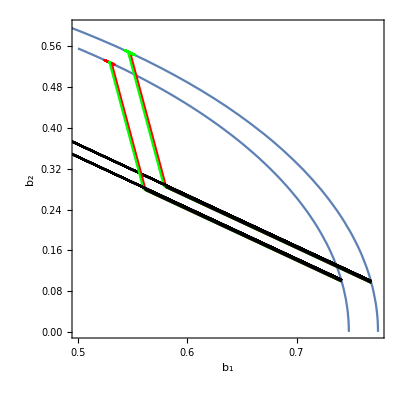

```mathematica
Show[{ContourPlot[x^2+y^2==X2,{x,0.5,Sqrt[X1]},{y,0,0.6}],
ContourPlot[x^2+y^2==X1,{x,0,Sqrt[X1]},{y,0,Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2],Evaluate[{x1[t],y1[t]}/.sol3],Evaluate[{x2[t],y2[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol2],Evaluate[{x2[t],y2[t]}/.sol3]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black},AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},FrameTicks->{{0.5,0.55,0.6,0.65,0.7,0.75},Automatic,None,None},FrameTicksStyle->Directive[16],RotateLabel->False]
```

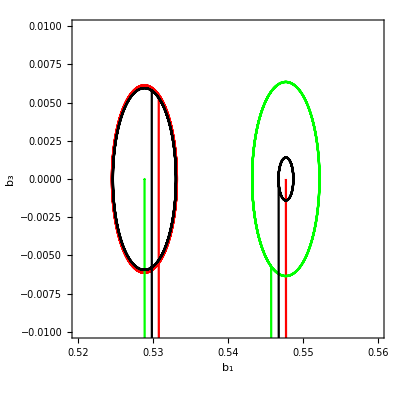

```mathematica
Show[{ContourPlot[x^2+y^2==X2,{x,0.52,0.56},{y,-0.01,+0.01}],
ContourPlot[x^2+y^2==X1,{x,0,Sqrt[X1]},{y,0,Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],z1[t]}/.sol1],Evaluate[{x1[t],z1[t]}/.sol2],Evaluate[{x1[t],z1[t]}/.sol3],Evaluate[{x2[t],z2[t]}/.sol1],Evaluate[{x2[t],z2[t]}/.sol2],Evaluate[{x2[t],z2[t]}/.sol3]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black},AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",18,Italic],Style["b_3",18,Italic]},FrameTicks->{Automatic,Automatic,None,None},FrameTicksStyle->Directive[16],RotateLabel->False]
```

```mathematica
Show[{ContourPlot3D[x^2+y^2+z^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]},{z,-Sqrt[X1],Sqrt[X1]},ContourStyle->{Opacity[1],Green},Mesh->None,AxesLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic],Style["b_3",18,Italic]}],ParametricPlot3D[{Evaluate[{x1[t],y1[t],z1[t]}/.sol1]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Red]},Ticks->None]
```

-Graphics3D-

```mathematica
Show[%40,BoxStyle->Directive[Dashed,Gray]]
```

-Graphics3D-

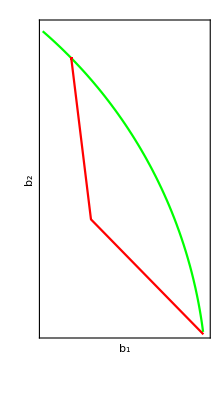

```mathematica
Show[{
ContourPlot[x^2+y^2==X1,{x,0.5,Sqrt[X1]},{y,0.1,0.6},ContourStyle->Green],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red},AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},RotateLabel->False,AspectRatio->Automatic,FrameTicksStyle->Directive[18],FrameTicks->{{None,None},{None,None}}]
```

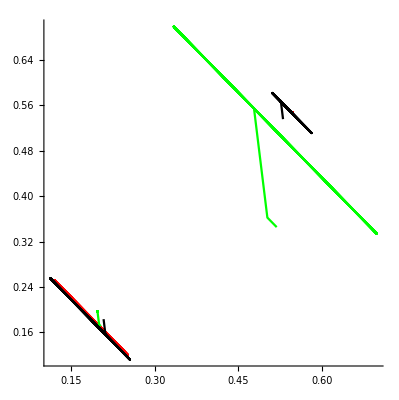

```mathematica
Show[ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2],Evaluate[{x1[t],y1[t]}/.sol3],Evaluate[{x2[t],y2[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol2],Evaluate[{x2[t],y2[t]}/.sol3]},{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black},FrameLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold]},RotateLabel->False]]
```

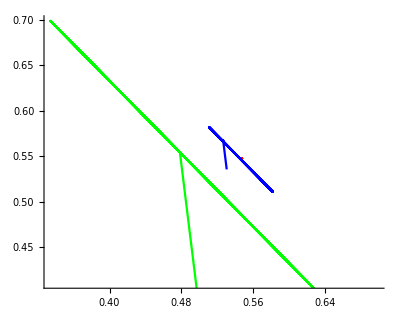

```mathematica
Show[ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2],Evaluate[{x1[t],y1[t]}/.sol3]},{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Blue},FrameLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold]},RotateLabel->False]]
```

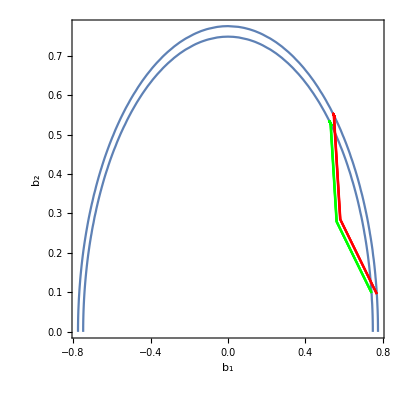

```mathematica
Show[{ContourPlot[x^2+y^2==X2,{x,-Sqrt[X1],Sqrt[X1]},{y,0,Sqrt[X1]}],
ContourPlot[x^2+y^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,0,Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2],Evaluate[{x2[t],y2[t]}/.sol2],Evaluate[{x1[t],y1[t]}/.sol3],Evaluate[{x2[t],y2[t]}/.sol3]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green},AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold]},RotateLabel->False]
```

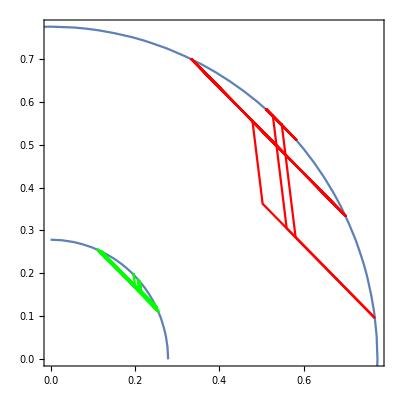

```mathematica
Show[{ContourPlot[x^2+y^2==X2,{x,-0,Sqrt[X1]},{y,-0,Sqrt[X1]}],ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol1],{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Red,AxesOrigin->{0.5,0.5}],
ContourPlot[x^2+y^2==X1,{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]}],ParametricPlot[Evaluate[{x2[t],y2[t]}/.sol1],{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Green,AxesOrigin->{0.5,0.5}],ParametricPlot[Evaluate[{x2[t],y2[t]}/.sol2],{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Green,AxesOrigin->{0.5,0.5}],
ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol2],{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Red,AxesOrigin->{0.5,0.5}],ParametricPlot[Evaluate[{x2[t],y2[t]}/.sol3],{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Green,AxesOrigin->{0.5,0.5}],
ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol3],{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Red,AxesOrigin->{0.5,0.5}]
}]
```

```mathematica
N[t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]
```

0.404843

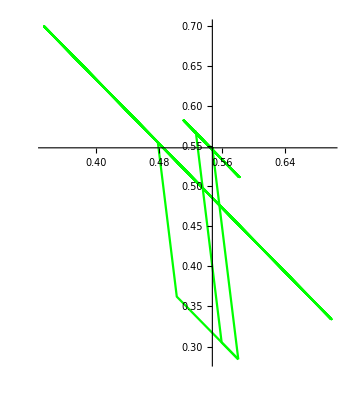

```mathematica
Show[{
ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol1],{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Green],
ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol2],{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Green],
ParametricPlot[Evaluate[{x1[t],y1[t]}/.sol3],{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->Green]
},PlotRange->All]
```

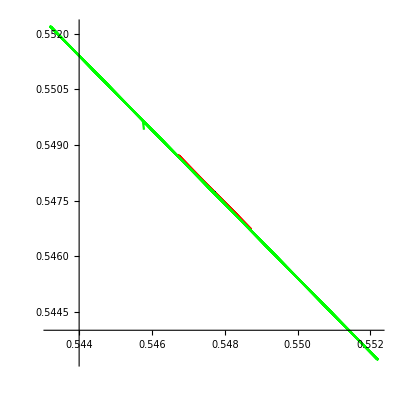

```mathematica
ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol3],Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x1[t],y1[t]}/.sol2]},{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Black,Green},PlotRange->All]
```

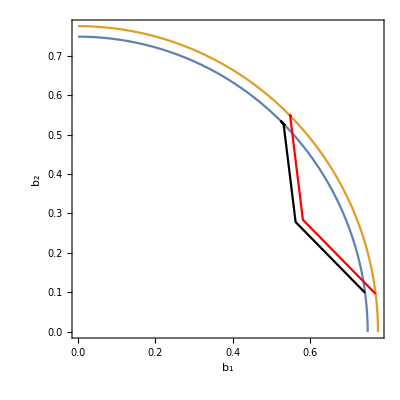

```mathematica
Show[{ContourPlot[{x^2+y^2==X2,x^2+y^2==X1},{x,-0,Sqrt[X1]},{y,-0,Sqrt[X1]}],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol1]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+2},PlotPoints->1000,PlotStyle->{Red,Black,Green},PlotRange->All,AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold]},RotateLabel->False]
```

```mathematica
plot1=ParametricPlot3D[{Evaluate[{x1[t],y1[t],z1[t]}/.sol1],Evaluate[{x1[t],y1[t],z1[t]}/.sol2],Evaluate[{x1[t],y1[t],z1[t]}/.sol3]},{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]-0.0001,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black},PlotRange->All];
plot2=ParametricPlot3D[{Evaluate[{x2[t],y2[t],z2[t]}/.sol1],Evaluate[{x2[t],y2[t],z2[t]}/.sol2],Evaluate[{x2[t],y2[t],z2[t]}/.sol3]},{t,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]-0.0001,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+10},PlotPoints->1000,PlotStyle->{Red,Green,Black},PlotRange->All];
Show[{plot1,plot2},AxesLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold],Style["b_3",Large,Bold]}]
```

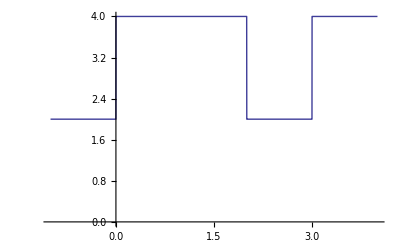

```mathematica
ω[w1_,w2_,t_,t1_,t2_]:=HeavisideTheta[-t]*w2+HeavisideTheta[t]* HeavisideTheta[t1-t]*w1+HeavisideTheta[(t1+t2)-t]*HeavisideTheta[t-t1]*w2+HeavisideTheta[t-(t1+t2)]*w1;
w1=4;
w2=2;
t1=2;
t2=1;
Plot[ω[w1,w2,t,t1,t2],{t,-1,t1+t2+1},AxesOrigin->{0,0}]
```

```mathematica
HeavisideTheta[400-(t1+t2)]
```

1

```mathematica
N[HeavisideTheta[0]]
```

HeavisideTheta[0.]

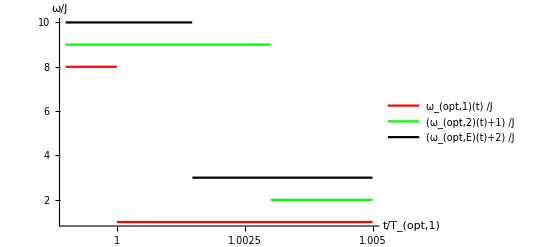

```mathematica
t1[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w1^2+1])*ArcSec[(w2-w1)*(w1-wi)/((1+w1*w2)*(1+w1*wi)-Sqrt[wi^2+1]/Sqrt[wf^2+1]*(1+w1^2)*(1+w2*wf))];
t2[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w2^2+1])*ArcSec[(w1-w2)*(wf-w2)/((1+w2^2)*Sqrt[wf^2+1]/Sqrt[wi^2+1]*(1+w1*wi)-(1+w1*w2)*(1+w2*wf))];
(*ω[w1_,w2_,t_,t1_,t2_]:= HeavisideTheta[t1-t]*w1+HeavisideTheta[t-t1]*w2;*)
ω[w1_,w2_,t_,t1_,t2_]:=HeavisideTheta[-t]*w2+HeavisideTheta[t]* HeavisideTheta[t1-t]*w1+HeavisideTheta[(t1+t2)-t]*HeavisideTheta[t-t1]*w2+HeavisideTheta[t-(t1+t2)]*w1;
Subscript[w, 1i]=8;
Subscript[w, 2i]=7.5;
Subscript[w, f]=1;
Subscript[w, min]=8;
Subscript[w, max]=1;
Plot[{ω[Subscript[w, max],Subscript[w, min],t*(t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]),t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]],ω[Subscript[w, max],Subscript[w, min],t*(t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]),t1[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 2i],Subscript[w, f]]]+1,ω[Subscript[w, max],Subscript[w, min],t*(t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]),(1.002885*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]),(0.1742622232216704*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]])]+2},{t,0.999,1.005},PlotRange->All,AxesOrigin->{0.999,0},PlotLegends->{Row[{Subscript["ω",Row[{Style["opt",Plain],",",1}]],"(t) /J"}],Row[{"(",Subscript["ω",Row[{Style["opt",Plain],",",2}]],"(t)+1) /J"}],Row[{"(",Subscript["ω",Row[{Style["opt",Plain],",","E"}]],"(t)+2) /J"}]},TicksStyle->{16,16},PlotStyle->{Red,Green,Black},AxesLabel->{Row[{"  t/",Subscript["T",Row[{Style["opt",Plain],",",1}]]}],"ω/J"},AxesStyle->{{18,Italic},{18,Italic}},Ticks->{{1,1.0025,1.005},Automatic}]
```

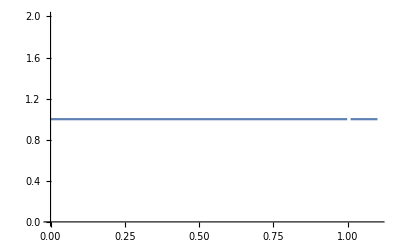

```mathematica
Plot[ω[Subscript[w, max],Subscript[w, min],t*(t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]),t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]],{t,0,1+0.1},AxesOrigin->{0,0},PlotRange->All]
```

```mathematica
N[t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]/(t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]])]
```

0.998588

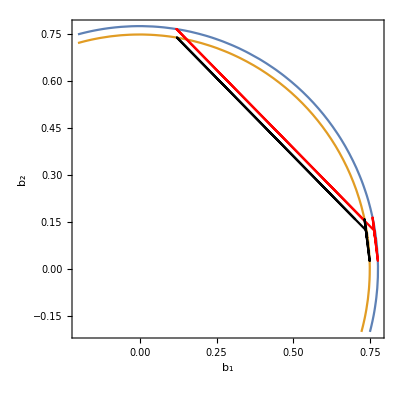

```mathematica
t1[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w1^2+1])*ArcSec[(w2-w1)*(w1-wi)/((1+w1*w2)*(1+w1*wi)-Sqrt[wi^2+1]/Sqrt[wf^2+1]*(1+w1^2)*(1+w2*wf))];
t2[w1_,w2_,wi_,wf_]:=1/(2*Sqrt[w2^2+1])*ArcSec[(w1-w2)*(wf-w2)/((1+w2^2)*Sqrt[wf^2+1]/Sqrt[wi^2+1]*(1+w1*wi)-(1+w1*w2)*(1+w2*wf))];
(*ω[w1_,w2_,t_,t1_,t2_]:= HeavisideTheta[t1-t]*w1+HeavisideTheta[t-t1]*w2;*)
ω[w1_,w2_,t_,t1_,t2_]:= HeavisideTheta[t1-t]*w1+HeavisideTheta[(t1+t2)-t]*HeavisideTheta[t-t1]*w2+HeavisideTheta[t-(t1+t2)]*w1;
Subscript[w, 1i]=8;
Subscript[w, 2i]=7.5;
Subscript[w, f]=1;
Subscript[w, min]=8;
Subscript[w, max]=1;
j=0.13;
X1=0.6;
Temperature=Sqrt[Subscript[w, 1i]^2+1]/(ArcTanh[-Sqrt[X1]]);
X2=(Tanh[Sqrt[Subscript[w, 2i]^2+1]/Temperature])^2;
E10=Sqrt[X1*(Subscript[w, 1i]^2+1)];
E20=Sqrt[X2*(Subscript[w, 2i]^2+1)];
sol1=NDSolve[{x1'[t]==2*z1[t],y1'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z1[t],z1'[t]==-2*x1[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y1[t],x2'[t]==2*z2[t],y2'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z2[t],z2'[t]==-2*x2[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y2[t],x1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1),y1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1)/Subscript[w, 1i],z1[0]==0,x2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1),y2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1)/Subscript[w, 2i],z2[0]==0},{x1,y1,z1,x2,y2,z2},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+2},MaxSteps->∞];
Show[{ContourPlot[{x^2+y^2==X1,x^2+y^2==X2},{x,-0.2,Sqrt[X1]},{y,-0.2,Sqrt[X1]},AspectRatio->1],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol1]},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+2},PlotPoints->1000,PlotStyle->{Red,Black},PlotRange->All,AxesOrigin->{0,0}]},FrameStyle->Directive[FontSize->16], FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},RotateLabel->False]
```

```mathematica
Manipulate[sol1=NDSolve[{x1'[t]==2*z1[t],y1'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z1[t],z1'[t]==-2*x1[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y1[t],x2'[t]==2*z2[t],y2'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z2[t],z2'[t]==-2*x2[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y2[t],x1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1),y1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1)/Subscript[w, 1i],z1[0]==0,x2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1),y2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1)/Subscript[w, 2i],z2[0]==0},{x1,y1,z1,x2,y2,z2},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+2},MaxSteps->∞];
Show[{ContourPlot[{x^2+y^2==X1,x^2+y^2==X2},{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]},AspectRatio->1],ParametricPlot[{Evaluate[{x1[t],y1[t]}/.sol1],Evaluate[{x2[t],y2[t]}/.sol1]},{t,0,T},PlotPoints->1000,PlotStyle->{Red,Black},PlotRange->All,AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold]},RotateLabel->False],{j,0.001,1.1,0.01},{T,0.01,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+2}]
```

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.001×10^-8 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.001×10^-8 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.001×10^-8 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.001×10^-8 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

NDSolve::dsvar: 0. cannot be used as a variable.

ReplaceAll::reps: {NDSolve[« 1 »]} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.001×10^-8 cannot be used as a variable.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NDSolve::dsvar: 1.001×10^-8 cannot be used as a variable.

General::stop: Further output of NDSolve :: dsvar will be suppressed during this calculation.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll :: reps will be suppressed during this calculation.

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[], List[Rule[DisplayFunction, Identity], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[Rule[.

```mathematica
Manipulate[sol1=NDSolve[{x1'[t]==2*z1[t],y1'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z1[t],z1'[t]==-2*x1[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y1[t],x2'[t]==2*z2[t],y2'[t]==-2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*z2[t],z2'[t]==-2*x2[t]+2*ω[Subscript[w, max],Subscript[w, min],t,j*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]],(1-j)*t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]]*y2[t],x1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1),y1[0]==E10*(Subscript[w, 1i])/((Subscript[w, 1i])^2+1)/Subscript[w, 1i],z1[0]==0,x2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1),y2[0]==E20*(Subscript[w, 2i])/((Subscript[w, 2i])^2+1)/Subscript[w, 2i],z2[0]==0},{x1,y1,z1,x2,y2,z2},{t,0,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+t2[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]+2},MaxSteps->∞];
Show[{ContourPlot[{x^2+y^2==X1,x^2+y^2==X2},{x,-Sqrt[X1],Sqrt[X1]},{y,-Sqrt[X1],Sqrt[X1]},AspectRatio->1],ListPlot[{Evaluate[{x1[T],y1[T]}/.sol1][[1]],Evaluate[{x2[T],y2[T]}/.sol1][[1]]},PlotStyle->{Red,Black},PlotRange->All,AxesOrigin->{0,0}]},FrameLabel->{Style["b_1",Large,Bold],Style["b_2",Large,Bold]},RotateLabel->False],{j,0.001,1,0.01},{T,0.01,t1[Subscript[w, max],Subscript[w, min],Subscript[w, 1i],Subscript[w, f]]}]
```

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[List[], List[], List[]], List[Rule[DisplayFunction, Identity], Rule[PlotRangePadding, List[List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]], List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 1], List[0.`, 1]]], Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 1], List[0.`, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]], List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]], Rule[Ticks, List[Automatic, Automatic]]]]}, FrameLabel → {StyleBox[.

NDSolve::underdet: There are more dependent variables, {ω[w_max, w_min, t, 0.001\ t1[w_max, w_min, w_i, w_f], 0.999\ t1[w_max, w_min, w_i, w_f] + t2[w_max, w_min, w_i, w_f]], x1[t], x2[t], y1[t], y2[t], z1[t], z2[t]}, than equations, so the system is underdetermined.

ContourPlot::plln: Limiting value -√X1 in {x, -√X1, √X1} is not a machine-sized real number.

ReplaceAll::reps: NDSolve[{SuperscriptBox[ is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

Show::gcomb: Could not combine the graphics objects in {ContourPlot[{x^2 + y^2 == X1, x^2 + y^2 == X2}, {x, -√X1, √X1}, {y, -√X1, √X1}, AspectRatio → 1], GraphicsBox[List[List[], List[], List[]], List[Rule[DisplayFunction, Identity], Rule[PlotRangePadding, List[List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]], List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]], Rule[AxesOrigin, List[0, 0]], Rule[PlotRange, List[List[0.`, 1], List[0.`, 1]]], Rule[DisplayFunction, Identity], Rule[AspectRatio, NCache[Power[GoldenRatio, -1], 0.6180339887498948`]], Rule[Axes, List[True, True]], Rule[AxesLabel, List[None, None]], Rule[AxesOrigin, List[0, 0]], RuleDelayed[DisplayFunction, Identity], Rule[Frame, List[List[False, False], List[False, False]]], Rule[FrameLabel, List[List[None, None], List[None, None]]], Rule[FrameTicks, List[List[Automatic, Automatic], List[Automatic, Automatic]]], Rule[GridLines, List[None, None]], Rule[GridLinesStyle, Directive[GrayLevel[0.5`, 0.4`]]], Rule[Method, List[]], Rule[PlotRange, List[List[0.`, 1], List[0.`, 1]]], Rule[PlotRangeClipping, True], Rule[PlotRangePadding, List[List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]], List[Scaled[Skeleton[1]], Scaled[Skeleton[1]]]]], Rule[Ticks, List[Automatic, Automatic]]]]}, FrameLabel → {StyleBox[.

```mathematica
ContourPlot[{x^2+y^2==X1},{x,0.4,Sqrt[X1]},{y,0.1,Sqrt[X1]-0.1},AspectRatio->1,FrameLabel->{Style["b_1",18,Italic],Style["b_2",18,Italic]},RotateLabel->False,FrameTicks->None]
```